# Rosseler System Intuitive Understanding

## Equilibrium Solutions Forward/Backwards Time

Definition
The equilibrium solutions of an autonomous ODE y'=f(y) are the solutions of f(y_eq)=0.

Back to the Rosseler ODE system 
	-Graphics-	
The equilibrium solutions for Rosseler (with the default initial conditions) are computed below

```mathematica
Clear[ f,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
EqSols={y1,y2,y3}/.Solve[f[{0.2,0.2,5.7}][{y1,y2,y3}]==0,{y1,y2,y3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.0070262,-0.035131,0.035131},{5.69297,-28.4649,28.4649}}

Here is a plot of the equilibrium solutions and a similar solution to the one we saw before.

```mathematica
Clear[y0, ySol]
y0={1.1,1.2,5.4};
{t0,TMax}={0,123};
ySol = NDSolveValue[{y'[t]==f[{0.2,0.2,5.7}][y[t]],y[t0]==y0},y,{t,t0, TMax}];
Show[
ParametricPlot3D[ySol[t],{t,t0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin],
Graphics3D[{Cyan,PointSize[0.02],Point[EqSols]}]
]
```

Definition
The autonomous ODE y'=-f(y) is the time reversal of the ODE y'=f(y).

```mathematica
Clear[y0, yBackSol]
y0={1.1,1.2,5.4};
{t0,TMax}={0,12};
yBackSol = NDSolveValue[{y'[t]==-f[{0.2,0.2,5.7}][y[t]],y[t0]==y0},y,{t,t0, TMax}];
Show[
ParametricPlot3D[{ySol[t],yBackSol[t]},{t,t0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin],
Graphics3D[{Cyan,PointSize[0.02],Point[EqSols]}]
]
```

-Graphics3D-

What happens if we go forwards from near the “big” 
		{5.69297,-28.4649,28.4649}
equilibrium solution?

```mathematica
Clear[y0, ySol]
y0={5.6,-28,28};
{t0,TMax}={0,20};
ySol = NDSolveValue[{y'[t]==f[{0.2,0.2,5.7}][y[t]],y[t0]==y0},y,{t,t0, TMax}];
Show[
ParametricPlot3D[{ySol[t]},{t,t0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin],
Graphics3D[{Cyan,PointSize[0.02],Point[EqSols]}]
]
```

-Graphics3D-

What happens if we go forwards from near the “small” 
		{0.0070262,-0.035131,0.035131}
equilibrium solution?

```mathematica
Clear[y0, ySol]
y0={0,-0,0.03};
{t0,TMax}={0,400};
ySol = NDSolveValue[{y'[t]==f[{0.2,0.2,5.7}][y[t]],y[t0]==y0},y,{t,t0, TMax}];
Show[
ParametricPlot3D[{ySol[t]},{t,t0,TMax},PlotRange->All,PlotPoints->2123,
PlotStyle->Thin],
Graphics3D[{Cyan,PointSize[0.02],Point[EqSols]}]
]
```

-Graphics3D-

## Linearization about Eq Points: y'=f(y) f(y_eq)=0

Write y(t)=y_eq+z(t) for a solution of the autonomous ODE y'=f(y) near an equilibrium point f(y_eq)=0.  For smooth functions f the Taylor series stuff from Calculus III gives
	(y_eq+z(t))'=f(y_eq+z(t))=f(y_eq)+Df(y_eq).z(t)+…=0+Df(y_eq).z(t)+…
where the missing terms (hiding in the ellipsis) contain second and higher derivatives at evaluated at y_eq. The first missing term is 
	DDf(y_eq).z(t).z(t)
and ||DDf(y_eq).z(t).z(t)||≤C||z(t)(||)^2
The second missing term is 
	DDDf(y_eq).z(t).z(t).z(t)
and ||DDDf(y_eq).z(t).z(t).z(t)||≤C||z(t)(||)^3. All these terms are very small when z is small. Solutions of y'=f(y) near an equilibrium solution y_eq look like
	y(t)=y_eq+z(t)
where z satisfies the linear constant coefficient system
	z'(t)=Df(y_eq).z(t)

Definition
The linearization of y'=f(y) near an equilibrium solution f(y_eq)=0 is the  constant coefficient system of ODEs
	z'(t)=Df(y_eq).z(t)

Lets see how well this approximation works for our test system near the small 
	{0.0070262,-0.035131,0.035131}
equilibrium solution. It is easy to compute the derivatives.

```mathematica
Clear[ f,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
Df=D[f[{a,b,c}][{y1,y2,y3}],{{y1,y2,y3}}]
MatrixForm[Df]
SmallEq={y1,y2,y3}/.Solve[f[{0.2,0.2,5.7}][{y1,y2,y3}]==0,{y1,y2,y3}][[1]]
```

{{0,-1,-1},{1,a,0},{y3,0,-c+y1}}

(0 | -1 | -1
1 | a | 0
y3 | 0 | -c+y1)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{0.0070262,-0.035131,0.035131}

To get the matrix we are looking for we need to plug the equilibrium solution and parameters into the recipe for the derivative. The solution and the linearized approximation stay together for a long time!

```mathematica
Clear[a,b,c,x,y,z,y1,y2,y3,t]
Subber={a->0.2,b->0.2,c->5.7,
y1->0.007026204834100129,
y2->-0.035131024170500645,
y3->0.035131024170500645};
yEq={y1,y2,y3}/.Subber;
A=Df/.Subber;
Eigenvalues[A]
y0={0.005,-0.1,0.1}; TMax=12;
z0=y0-{y1,y2,y3}/.Subber;
ySol=NDSolveValue[{y'[t]==f[{0.2,0.2,5.7}][y[t]],y[0]==y0},y,{t,0,TMax}];
zSol=NDSolveValue[{z'[t]==A.z[t],z[0]==z0},z,{t,0,TMax}];
ParametricPlot3D[{ySol[t],zSol[t]+yEq},{t,0, TMax},BoxRatios->{1, 1, 1}]
```

{-5.68698+0. ⅈ,0.0970009+0.995193 ⅈ,0.0970009-0.995193 ⅈ}

-Graphics3D-

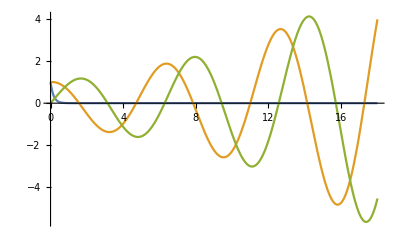

```mathematica
Plot[ {E^(-6 t),Re[E^((0.1+I)t)],Im[E^((0.1+I)t)]},{t, 0, 18},
PlotRange->All]
```

If you run it long enough (or start further from the equilibrium point) they will separate.

```mathematica
A
```

DDf

```mathematica
Subber={a->0.2,b->0.2,c->5.7,
y1->0.007026204834100129,
y2->-0.035131024170500645,
y3->0.035131024170500645};
yEq={y1,y2,y3}/.Subber;
A=Df/.Subber;
y0={0.005,-0.1,0.1}; TMax=30;
z0=y0-{y1,y2,y3}/.Subber;
ySol=NDSolveValue[{y'[t]==f[{0.2,0.2,5.7}][y[t]],y[0]==y0},y,{t,0,TMax}];
zSol=NDSolveValue[{z'[t]==A.z[t],z[0]==z0},z,{t,0,TMax}];
ParametricPlot3D[{ySol[t],zSol[t]+yEq},{t,0, TMax},BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Analytic Solutions of z'=A.z

The eigenvalues of A determine the behavior of solutions of z'=A.z.

### Linear Algebra. Reminders

Definition (Reminder from Linear Algebra)
(λ,v) is an eigenvalue-eigenvector pair for a matrix A if 
	A.v=λ v

Property (Reminder from Linear Algebra)
Eigenvalues are either real or form complex conjugate pairs
	λ=α±I β and v=a+±I b
for a real matrix A.

### Ordinary Differential Equations. Reminders

It is easy to see that a linearly independent set of n eigenvectors of A gives an n parameter solution of z'=A.z.

Observation (Reminder from ODE)
If (λ,v) is an eigenvalue-eigenvector pair for A then
	z(t)=ⅇ^(λ t)v 
satisfies z'(t)=A.z(t)

Observation  (Reminder from ODE)
If we have n eigenvalue-eigenvector pairs (λ_i,v_i)  for A then
	z(t)=∑_(i=1)^n c_i ⅇ^(λ_i t)v_i 
satisfies z'(t)=A.z(t) for any choice of c={c_1,c_2,…,c_n}

Observation  (Reminder from ODE)
A complex conjugate eigen-pair λ=α±I β and v=a+±I b gives a pair of linearly independent solutions
	y_+=ⅇ^((α+ I β) t)(a++I b) and y_-=ⅇ^((α- I β) t)(a+-I b) 
an equivalent linearly independent pair of solutions is 
	y_re=Re(ⅇ^((α+ I β) t)(a++I b)) and y_im=Im(ⅇ^((α+ I β) t)(a++I b))  
These real solutions are simply
	y_re | = | ⅇ^(α t) | ( | cos(β t)a | - | sin(β t)b | )
y_im | = | ⅇ^(α t) | ( | sin(β t)a | + | cos(β t)b | )

### Ordinary Differential Equations. Probably New

Interpretation  (Should be from ODE)
For y'=A.y:
1) Parts of solutions from eigenvalues with positive eigenvalues grow exponentially.
2) Parts of solutions from eigenvalues with negative eigenvalues decay exponentially.
3) Parts of solutions from complex eigenvalue pairs α±I β behave like 
	ⅇ^(α t)sin(β t) or ⅇ^(α t)cos(β t).
They grow or decay exponentially like ⅇ^(α t)while wiggling sinusoidally with period (2π)/β.

Informal Definition
An equilibrium point y_eq for y'=f(y) is stable if all solutions starting near y_eq approach y_eq as t→∞. An equilibrium point is unstable if there are solutions starting near y_eq that do not stay near y_eq.

Theorem
An equilibrium point y_eq for y'=f(y) is stable if all the eigenvalues of Df(y_eq) have negative real part. An equilibrium point is unstable if at least one eigenvalue of Df(y_eq) has a positive real part.

## Equilibrium Points of the Rosseler System: Standard Parameters

So what can we say about the two equilibrium points of the our Rosseler system.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
{ySmall,yBig}={y1,y2,y3}/.Solve[f[{0.2,0.2,5.7}][{y1,y2,y3}]==0,{y1,y2,y3}];
TableForm[Map[Eigenvalues[df[StdParams][#]]&,{ySmall,yBig}],
TableHeadings->{{"y_small","y_big"},Automatic}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

| 1 | 2 | 3
y_small | -5.68698+0. ⅈ | 0.0970009+0.995193 ⅈ | 0.0970009-0.995193 ⅈ
y_big | -4.59607×10^-6+5.42803 ⅈ | -4.59607×10^-6-5.42803 ⅈ | 0.192983+0. ⅈ

The small equilibrium point is unstable it gets sucked in rapidly ⅇ^(-5.7 t) in one direction and spun out slowly ⅇ^(0.097t) in two directions: each spin takes roughly 2π time units.

The big equilibrium point is also unstable it gets pushed out relatively slowly ⅇ^(0.19t) in one direction and spun in very slowly ⅇ^(-4.6×10^-6 t) in two directions: each spin takes roughly 2π/5.428 time units.

## Central equilibrium of Rosseler System: Standard Parameters

So what can we say about the two equilibrium points of the our Rosseler system.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
Quiet[{ySmall,yBig}={y1,y2,y3}/.Solve[f[{0.2,0.2,5.7}][{y1,y2,y3}]==0,{y1,y2,y3}];]
```

```mathematica
y0=ySmall+{0.3,0.2,0.3}; TMax=123;
ASmall=df[StdParams][ySmall];
ySol=NDSolveValue[{y'[t]==f[StdParams][y[t]],y[0]==y0},y,{t, 0, TMax}]
Pic3D=Show[
Graphics3D[{PointSize[0.02],Cyan, Point[ySmall]}],
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->123,PlotStyle->Thin]
];
Animate[Show[Pic3D,ViewPoint->15{Cos[θ],Sin[θ],2},
PlotRange->20{{-1,1},{-1,1},{0,1}}],{θ,0, 2π}]
```

InterpolatingFunction[{{0., 123.}}, <>]

```mathematica
Hmm=Table[
Show[Pic3D,Graphics3D[{Red, PointSize[0.02],Point[ySol[t]]}]],
{t,0, TMax, 0.2}]
SetDirectory["C:\\Users\\struther\\Desktop"]
Export["Hmm.gif",Hmm]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

C:\Users\struther\Desktop

Hmm.gif

```mathematica
y0=ySmall+{0.3,0.2,0.3}; TMax=123;
ASmall=df[StdParams][ySmall];
ySol=NDSolveValue[{y'[t]==f[StdParams][y[t]],y[0]==y0},y,{t, 0, TMax}];
Pic3D=Show[
Graphics3D[{PointSize[0.02],Cyan, Point[ySmall]}],
ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All,PlotPoints->123,PlotStyle->Thin]
]
{{λ1,λ2,λ3},{v1,v2,v3}}=Chop[Eigensystem[ASmall]]
```

-Graphics3D-

{{-5.68698,0.0970009+0.995193 ⅈ,0.0970009-0.995193 ⅈ},{{0.168236,-0.0285777,0.985332},{0.70728,-0.0727751-0.703164 ⅈ,0.00416832-0.00071646 ⅈ},{0.70728,-0.0727751+0.703164 ⅈ,0.00416832+0.00071646 ⅈ}}}

```mathematica
λ2
```

0.0970009+0.995193 ⅈ

```mathematica
a=Re[v2]; b=Im[v2];
Show[Pic3D,
Graphics3D[ {
{ Green, Arrow[ {ySmall+10v1,ySmall}],Arrow[ {ySmall-10v1,ySmall}]},
{ Red, Arrow[ {ySmall,ySmall+10a}], Arrow[ {ySmall,ySmall-10a}],
Arrow[ {ySmall,ySmall+10b}], Arrow[ {ySmall,ySmall-10b}]}
}]
]
```

-Graphics3D-

```mathematica
a
b
```

{0.70728,-0.0727751,0.00416832}

{0,-0.703164,-0.00071646}

{56.3123,20.9919}

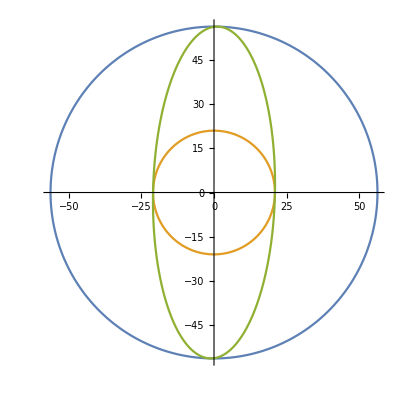

0.372776

```mathematica
B= {
{21.,1},
{0.2,56.3}
};
{σ1,σ2}=SingularValueList[B]
ParametricPlot[ {σ1 {Cos[θ],Sin[θ]},σ2 {Cos[θ],Sin[θ]},B.{Cos[θ], Sin[θ]}},{θ,0, 2π}]
σ2/σ1
```